# Little Tests

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=1;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

ia=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
icolor=reduire[clean@Import[pathResult],reduce];

(*{1,44},{1,102} arbitrary size to make the method faster *)
dim=ImageDimensions[ia];
nx=dim[[1]]/2/reduce;
ny=dim[[2]]/2/reduce;

{ia,ib,icolor}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,icolor}
ImageDimensions[#]&/@{ia,ib,icolor}
```

{-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45}}

## Little Tests

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

```mathematica
(*Test*)
row=20;
lvlmin=1;
lvlmax=4;

pyrfiab=pyrfi[ia,ib,row,lvlmax];
```

#### Little Test: Test Row

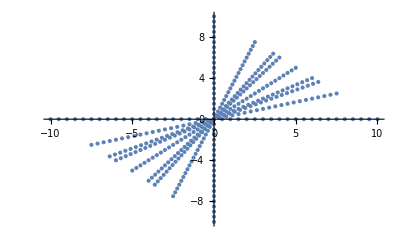

```mathematica
(* Creating list of initial Values *)
rangev0=Range[-10,10,0.5];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
ListPlot[listv0]
```

```mathematica
(* Initialixze *)
testRow=20;

steps=1;
e=0.00001;
lvlmin=1;
lvlmax=3;

ic=ib;

{ia, ic,icolor}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*See*)
pyrfiac=pyrfi[ia,ic,testRow,lvlmax];
Plot[{pyrfiac[[lvlmin,1,1]][x],pyrfiac[[lvlmin,2,1]][x]},{x,1,103}];
Plot[{pyrfiac[[lvlmax,1,1]][x],pyrfiac[[lvlmax,2,1]][x]},{x,1,103}];
Plot[{pyrfiac[[lvlmax,1,2]][x],pyrfiac[[lvlmax,2,2]][x],-e,+e},{x,1,103}];
```

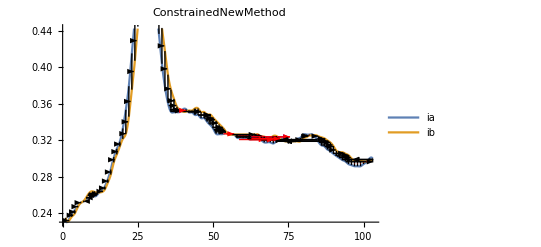

```mathematica
(* Row test solution *)
seeAllLine[listv0,Range[1,103,steps],pyrfiac[[lvlmin;;lvlmin]],e*2^(-lvlmin+1),"ConstrainedNewMethod"]
```

```mathematica
solminmax=lineTest[listv0,Range[1,103,steps],pyrfiac[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"];
```

```mathematica
solminmin=lineTest[listv0,Range[1,103,steps],pyrfiac[[lvlmin;;lvlmin]],e*2^(-lvlmin+1),"ConstrainedNewMethod"];
```

```mathematica
solmaxmax=lineTest[listv0,Range[1,103,steps],pyrfiac[[lvlmax;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"];
```

```mathematica
Dimensions[Select[solminmax,#[[3]]=="converged" &]]
Dimensions[Select[solminmin,#[[3]]=="converged" &]]
Dimensions[Select[solmaxmax,#[[3]]=="converged" &]]
```

{64,4}

{96,4}

{62,4}

```mathematica
ListAnimate[pixelIterGraphics[10,100,listv0,5, lvlmax,pyrfiac[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"]]
```

#### Little Test: Full image

```mathematica
combinePV[realPV_]:=Block[{srtDistinctPV,newPV,i,c,sum,solution},(

srtDistinctPV=Sort[DeleteDuplicates[Floor[realPV[[All,1]]]]];

newPV=SortBy[Flatten[{Floor[realPV[[All,1]]],realPV[[All,2]]},{{2},{1}}],First];

i=1;

Table[
c=0;
sum=0;

While[newPV[[i,1]]==p, 
sum=newPV[[i,2]]+sum;
c=c+1;
i=i+1;
solution={p,sum/c}
];
solution

,{p,srtDistinctPV}]

)]
```

```mathematica
(* Stereo Depth result *)
steps=1;
linemax=45;

e=0.0001;
lvlmin=1;
lvlmax=1;

depth=stereoDepth[listv0,ia,ic,lvlmax,{lvlmin,lvlmax},Range[1,103,steps],Range[1,linemax],e,"ConstrainedNewMethod"];
Dimensions[depth]
```

{45,103,5}

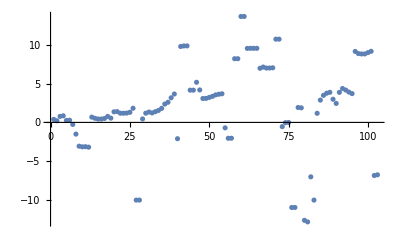

```mathematica
ListPlot[depth[[testRow,All,1]]]
```

```mathematica
(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
,{r,linemax}];

Dimensions[resTable]
```

{45}

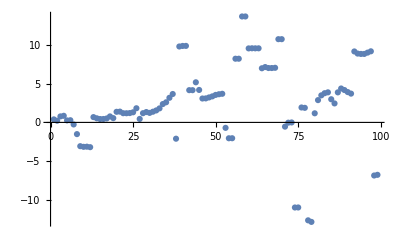

```mathematica
ListPlot[resTable[[testRow,All,1]]]
```

```mathematica
(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,-resTable[[r,All,1]]}]
,{r,linemax}];

Dimensions[realPVTable]
realPVTable;
```

{45}

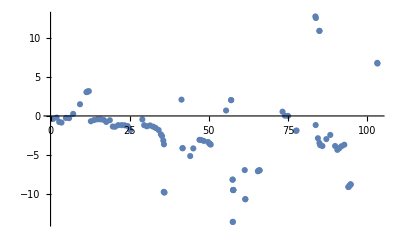

```mathematica
ListPlot[realPVTable[[testRow,All]]]
```

```mathematica
(* We combine solutions for each coordinate *)
resPVTable=Table[
combinePV[realPVTable[[r]]]

,{r,linemax}];
Dimensions[resPVTable]
```

Part::partw: Part 91 of {{12,11.4028},{12,11.5874},{12,11.8967},{12,11.9014},{12,11.9412},{12,11.9565},{12,11.9825},{13,-0.543623},{13,12.1139},{13,12.1205},«80»} does not exist.

Part::partw: Part 86 of {{12,12.1931},{12,12.2553},{12,12.3453},{12,12.3797},{13,-0.769466},{13,12.4186},{13,12.4364},{13,12.4712},{13,12.4858},{13,12.4878},«75»} does not exist.

Part::partw: Part 90 of {{12,13.36},{12,13.3607},{12,13.4656},{12,13.4825},{12,13.5086},{13,-0.801019},{13,13.3403},{13,13.3404},{13,13.3418},{13,13.3418},«79»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{45}

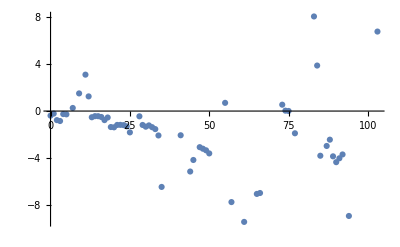

```mathematica
ListPlot[resPVTable[[testRow,All]]]
```

```mathematica
createReplaceValues[resPVTable_]:=Block[{rows},(
rows=Length[resPVTable];
Flatten[Table[
Thread[Thread[{resPVTable[[r,All,1]],r}-0.5]->resPVTable[[r,All,2]]]
,{r,rows}],1]
)]
```

```mathematica
values=createReplaceValues[resPVTable];
Dimensions[values]
```

{2786}

```mathematica
values[[103*3]]
```

{47.5,5.5}→-3.29733

```mathematica
im=Image[Table[0,{y,linemax},{x,103}]]
```

-Graphics-

```mathematica
imm=ReplaceImageValue[im, values[[1;;103*27]]]

imm=ImageAdjust[imm]
```

-Graphics-

-Graphics-

```mathematica
ImageReflect[imm]
```

-Graphics-

```mathematica
GraphicsRow[{ImageReflect[imm], icolor}]
```

-Graphics-